```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts2\\"]
```

C:\Users\pglpm\repositories\genobayes\scripts2

```mathematica
bd[x_,a_,b_]=Assuming[0<x<1,FS@PDF[BetaDistribution[b,a],x]];
```

```mathematica
ClearAll[cd];cd[x_]=Assuming[Element[x,Reals],FS[PDF[CauchyDistribution[Log[1000],Log[1000]],x]]]
```

Log[1000]/(π (x^2-6 x Log[10]+18 Log[10]^2))

```mathematica
ClearAll[gd];gd[x_]=Assuming[x>0,FS[PDF[GammaDistribution[1,1000],x]]]
```

ⅇ^(-x/1000)/1000

```mathematica
viewpoint={2.0551050122481573,2.280771320151432,1.4228933810399123} (*for cauchy prior*)
```

{2.05511,2.28077,1.42289}

```mathematica
plot=Plot3D[cd[Log[t1]]*cd[Log[t2]]/(t1*t2),{t1,0,10},{t2,0,10},PlotRange->{0,0.001},Axes->True,PlotPoints->50,ViewPoint->Dynamic[viewpoint],ClippingStyle->None,Ticks->{Auto,Auto,None},Axes->Auto,AxesLabel->{Subscript[u,0],Subscript[u,1],Rotate["p"[HoldForm[Subscript[u,0]","Subscript[u,1]  "| "Style["I",Italic]]],Pi/2,{-2,0}]}]
```

-Graphics3D-

```mathematica
Export["testprioru.png",plot,(*"AllowRasterization"->True,*)ImageSize->a5rsize];
```

```mathematica
evidence[t_,s1_,s2_]:=(Gamma[Total@t]/(Times@@Gamma[t]))^2*
(Times@@Gamma[t+s1])/Gamma[Total@(t+s1)]*
(Times@@Gamma[t+s2])/Gamma[Total@(t+s2)];
```

```mathematica
(* A, SNP #6 *)
s1={1481,502};s2={2887,1159};
f=T@{s1,s2};numsnpvariants=2;
```

```mathematica
ClearAll[logpriortheta];logpriortheta[t_]:=(Total@Log@cd[Log[t]]-Total@Log[t]);
```

```mathematica
logprob[t_]:=Block[{r2=f+t},Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@t]-Total@LogGamma[t])+logpriortheta[t]];
```

```mathematica
evidence[{1,2},s1,s2]//N
```

2.58613892864967×10^-1544

```mathematica
bd[f_,t_]:=Times@@(PDF[BetaDistribution[Sequence@@t],f])
```

```mathematica
bd[0.5,{2,3}]
```

1.5

```mathematica
theta=FindArgMax[{logprob[{t1,t2}],t1>0&&t2>0},{{t1,1},{t2,1}}]
```

{0.123298,0.101888}

```mathematica
plot2=Plot3D[Exp[logprob[{t1,t2}]-logprob[theta]],{t1,0,10},{t2,0,10},PlotRange->{0,All},Axes->True,PlotPoints->50,ViewPoint->Dynamic[viewpoint],ClippingStyle->None,Ticks->{Auto,Auto,None},Axes->Auto,AxesLabel->{Subscript[u,0],Subscript[u,1],Rotate["p"[HoldForm[Subscript[u,0]","Subscript[u,1]  "| data"]],Pi/2,{-3,0}]}]
```

-Graphics3D-

```mathematica
Export["testpostu.png",plot2,(*"AllowRasterization"->True,*)ImageSize->a5rsize];
```

```mathematica
Plot3D[bd[{0.25,0.25},{t1,t2}],{t1,0,10},{t2,0,10},PlotRange->{0,All},Axes->True,PlotPoints->50,ViewPoint->Dynamic[viewpoint],ClippingStyle->None,Ticks->{Auto,Auto,None},Axes->Auto,AxesLabel->{Subscript[u,0],Subscript[u,1],Rotate["p"[HoldForm[Subscript[u,0]","Subscript[u,1]  "| data"]],Pi/2,{-3,0}]}]
```

-Graphics3D-

```mathematica
logprob[{0.1,0.1}]//N
```

-3551.4

```mathematica
logpriortheta[{0.1,0.1}]
```

-5.29852

```mathematica
FindMaximum[{Evaluate[Log@evidence[{t1,t2},s1,s2]],t1>0,t2>0},{t1,t2}]
```

{-3547.65,{t1→714.72,t2→266.145}}

```mathematica
bd[x_,a_,b_]=Assuming[0<x<1,FS@PDF[BetaDistribution[b,a],x]];
```

```mathematica
priora[x_,a_]:=NIntegrate[bd[x,a*q,a*(1-q)],{q,0,1},AccuracyGoal->+Infinity,PrecisionGoal->3,MaxRecursion->10^6];
```

```mathematica
prior[x_]:=NIntegrate[bd[x,a*q,a*(1-q)]*cd[a],{a,0,+Infinity},{q,0,1},AccuracyGoal->+Infinity,PrecisionGoal->3,MaxRecursion->10^6];
```

```mathematica
prior[0.5]
```

0.993171

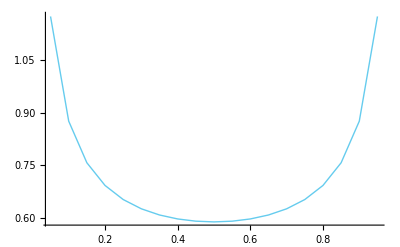

```mathematica
ListPlot[Table[{ii,priora[ii,2]},{ii,0.05,0.95,0.05}],Joined->True,PlotRange->All]
```

```mathematica
jpriora[x_,y_,a_]:=NIntegrate[bd[x,a*q,a*(1-q)]*bd[y,a*q,a*(1-q)],{q,0,1},AccuracyGoal->+Infinity,PrecisionGoal->3,MaxRecursion->10^6];
```

```mathematica
jprior[x_,y_]:=NIntegrate[bd[x,a*q,a*(1-q)]*bd[y,a*q,a*(1-q)]*gd[a],{a,0,+Infinity},{q,0,1},AccuracyGoal->+Infinity,PrecisionGoal->3,MaxRecursion->10^6];
```

```mathematica
ListPlot3D[Flatten[Table[{ii,jj,jpriora[ii,jj,10]},{ii,0.05,0.95,0.05},{jj,0.05,0.95,0.05}],1],PlotRange->Auto]
```

-Graphics3D-

```mathematica
Plot3D[jpriora[ii,jj,1],{ii,0.05,0.95},{jj,0.05,0.95},PlotRange->Auto]
```

$Aborted

```mathematica
jpriora[0.1,0.1,1]
```

0.764592

```mathematica
ListPlot3D[Flatten[Table[{ii,jj,jprior[ii,jj]},{ii,0.05,0.95,0.05},{jj,0.05,0.95,0.05}],1],PlotRange->All]
```

-Graphics3D-

```mathematica
ils[y_]=Assuming[0<y<1,FS[x/.Solve[LogisticSigmoid[x]==y,x,Reals][[1]]]]
```

Log[-y/(-1+y)]

```mathematica
Assuming[a>0&&0<q<1&&0<x<1&&0<y<1,FS[bd[x,a*q,a*(1-q)]*bd[y,a*q,a*(1-q)]*gd[a]]]
```

(ⅇ^(-a/1000) ((-1+x) (-1+y))^(-1+a q) (x y)^(-1+a-a q))/(1000 Beta[a-a q,a q]^2)

```mathematica
%687/. {x->0.4,y->0.3, a->97.954803160145,q->0.5}
```

1.84793×10^-6

```mathematica
mina=10^-6;maxa=10^6;const=Integrate[cd[a],{a,mina,maxa}];jpriorc[x_,y_]:=NIntegrate[bd[x,a*q,a*(1-q)]*bd[y,a*q,a*(1-q)]*gd[a]
,{a,mina,maxa},{q,0,1},AccuracyGoal->+Infinity,PrecisionGoal->2,MaxPoints->10^6]/const;
```

```mathematica
ClearAll[jpriorc,jpriorc2];
mina=10^-6;maxa=10^6;const=Integrate[cd[Log@a]/a,{a,mina,maxa}];jpriorc2[x_,y_]:=(xx=Min[x,y];yy=Max[x,y];If[yy>1-xx,xx2=1-yy;yy2=1-xx,xx2=xx;yy2=yy];jpriorc[xx2,yy2]);

jpriorc[xx_,yy_]:=jpriorc[xx,yy]=(x=N[xx];y=N[yy];NIntegrate[bd[x,a*q,a*(1-q)]*bd[y,a*q,a*(1-q)]*cd[Log[a*q]]*cd[Log[a*(1-q)]]/(a*q*(1-q))
,{a,2*mina,2*maxa},{q,mina/(mina+maxa),maxa/(mina+maxa)},AccuracyGoal->+Infinity,PrecisionGoal->1,MaxPoints->Auto]/const^2);
```

```mathematica
jpriorc[xx_,yy_]:=jpriorc[xx,yy]=(x=N[xx];y=N[yy];NIntegrate[bd[x,a*q,a*(1-q)]*bd[y,a*q,a*(1-q)]*cd[Log[a*q]]*cd[Log[a*(1-q)]]/(a*q*(1-q))
,{a,2*mina,2*maxa},{q,mina/(mina+maxa),maxa/(mina+maxa)},AccuracyGoal->+Infinity,PrecisionGoal->1,MaxPoints->Auto]/const^2);
```

```mathematica
jpriorc2[0.2,0.1]
```

0.135731

```mathematica
jpriorc2[0.1,0.2]
```

0.135731

```mathematica
datac=Flatten[Table[Print[ii];{ii,jj,jpriorc2[ii,jj]},{ii,5/100,95/100,90/100/30},{jj,5/100,95/100,90/100/30}],1];
```

```mathematica
ListPlot3D[datac,PlotRange->{0,10},Axes->True,ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
dataa=Flatten[Table[{ii,jj,jpriora[ii,jj,500]},{ii,0.05,0.95,0.05},{jj,0.05,0.95,0.05}],1];
```

```mathematica
plot=ListPlot3D[{datac,dataa},PlotRange->{0,Auto},ViewPoint->Dynamic[viewpoint],Ticks->{Auto,Auto,None},Axes->Auto,AxesLabel->{Subscript[f,HoldForm[O"|"a]],Subscript[f,HoldForm[O"|"b]],Rotate["p"[HoldForm[Subscript[f,"O |"a]","Subscript[f,O"|"b]"| initial info" ]],Pi/2,{1.25,0}]}
]
```

-Graphics3D-

```mathematica
dataa=Flatten[Table[{ii,jj,jpriora[ii,jj,50]},{ii,0.05,0.95,0.05},{jj,0.05,0.95,0.05}],1];
```

```mathematica
plot=ListPlot3D[dataa,PlotRange->{0,10},ViewPoint->Dynamic[viewpoint],Ticks->{Auto,Auto,None},Axes->Auto,AxesLabel->{Subscript[f,HoldForm[O"|"a]],Subscript[f,HoldForm[O"|"b]],Rotate["p"[HoldForm[Subscript[f,"O |"a]","Subscript[f,O"|"b]"| initial info" ]],Pi/2,{1.25,0}]}
]
```

-Graphics3D-

```mathematica
Export["test3dfa.png",plot,ImageSize->a5rsize*1.25];
```

```mathematica
Export["C:\\Users\\pglpm\\repositories\\genobayes\\prior3d.png",plot,ImageSize->a5rsize*1.5];
```

```mathematica
data=Import["dataset1_binarized.csv"][[2;;,2;;]];
```

```mathematica
allcouples=Flatten[Table[{ii,jj},{ii,93},{jj,ii+1,94}],1];
```

```mathematica
geneseq=Import["dataset1_binarized.csv"][[1,5;;]];
```

```mathematica
rsnp=RandomInteger[94]
```

84

```mathematica
symptoms={{1},{2}};snps={3+{rsnp}};
symptomvariants={{0},{1}};snpvariants={{0},{1}};
namesymptomvariants={"n","y"};
namesymptoms={"A","B","C"};
namesnps=Import["dataset1_binarized.csv"][[1,5;;]][[rsnp]];namesnpvariants={"0","1"};
numsymptoms=Length[symptoms];numsymptomvariants=Length[symptomvariants];numsnps=Length[snps];numsnpvariants=Length[snpvariants];namestatistics=Flatten@Table[ii<>jj,{ii,{"EV_","SD_","post.theta_","opt.theta_","max.spread_"}},{jj,namesymptomvariants}];
```

```mathematica
ClearAll[logpriortheta];logpriortheta[t_]:=cd[Total@t]-Log[Total@t];
```

```mathematica
<<conditional_freqs_1.m
```

```mathematica
spread=defaultspread;
```

```mathematica
condfreqstatistics[data,symptoms,symptomvariants,snps,snpvariants,namesymptoms,namesymptomvariants,namesnps,namesnpvariants,savedir,filename,logpriortheta,spread]//MF
```

((0.722309 | 0.726606
0.277691 | 0.273394
0.00807471 | 0.00815189
0.00807471 | 0.00815189
2221.33 | 2171.33
853.99 | 816.99
12.3292 | Null
4.98952 | Null
0.264813 | Null
0.264813 | Null)
(0.589542 | 0.578935
0.410458 | 0.421065
0.0088675 | 0.00902872
0.0088675 | 0.00902872
1813.66 | 1730.66
1262.72 | 1258.72
10.6573 | Null
7.7243 | Null
0.592722 | Null
0.592722 | Null))

```mathematica
sdata=data[[;;,Join[symptoms[[1]],snps[[1]]]]];
```

```mathematica
f=Table[Total[Boole/@Table[z==Join[symptomvariant,snpvariant],{z,sdata}]],{symptomvariant,symptomvariants},{snpvariant,snpvariants}]
```

{{1455,1868,503,542},{516,698,224,223}}

```mathematica
logprob[t_]:=Block[{r2=f+t},Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@t]-Total@LogGamma[t])+Total[logpriortheta[t]]];
```

```mathematica
logprob[{1,2}]//N
```

-3569.87

```mathematica
thetas=Array[t,numsymptomvariants]
```

{t[1],t[2]}

```mathematica
thetas=Table[Unique["t"],numsymptomvariants]
```

{t45,t46}

```mathematica
FindArgMax[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{41.0502,16.3425}

```mathematica
FindMaximum[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{-3565.28,{t45→41.0502,t46→16.3425}}

```mathematica
test[[2]]
```

{t45→41.0502,t46→16.3425}

```mathematica
theta=thetas/.FindMaximum[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]][[2]]
```

{{t39,t40}/.{t39,1092},{t39,t40}/.{t40,1661/4}}

```mathematica
fnew=f+theta
```

{{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343}}

```mathematica
nnew=Total[fnew]
```

{2028.39,2623.39,784.393,822.393}

```mathematica
Sequence@@T[T[fnew]/nnew]
```

Sequence[{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032}]

```mathematica
Sqrt[(Times@@fnew)/(nnew^2*(1+nnew))]
```

{0.00976638,0.00868929,0.0164497,0.01583}

```mathematica
Sqrt@T[((nnew-T@fnew)*T@fnew)/(nnew^2*(1+nnew))]
```

{{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583}}

```mathematica
Table[Null,numsnpvariants-1,numsymptomvariants]
```

{{Null,Null},{Null,Null},{Null,Null}}

```mathematica
T@Join[{theta},Table[Null,numsnpvariants-1,numsymptomvariants]]
```

{{41.0502,Null,Null,Null},{16.3425,Null,Null,Null}}

```mathematica
quantities={(*EV*)Sequence@@T[T[fnew]/nnew],(*STD*)Sequence@@Sqrt[T[((nnew-T@fnew)*T@fnew)/(nnew^2*(1+nnew))]],(*(*Quantiles*)Sequence@@(T@Table[Quantile[BetaDistribution[Sequence@@(Reverse[fnew[[;;,al]]])],quantiles],{al,binoutcomes+1}]),*)(*f+theta*)Sequence@@fnew,(*posterior theta*)Sequence@@T[Join[{theta},Table[Null,numsnpvariants-1,numsymptomvariants]]]}
```

{{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032},{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583},{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343},{41.0502,Null,Null,Null},{16.3425,Null,Null,Null}}

```mathematica
spread[q_]:=Max/@Abs@ArrayReshape[Table[(q[[co,x]]-q[[co,y]])/(q[[co+numsymptomvariants,x]]+q[[co+numsymptomvariants,y]]),{co,numsymptomvariants},{x,numsnpvariants-1},{y,x+1,numsnpvariants}],{numsymptomvariants,Binomial[numsnpvariants,2]}]
```

```mathematica
spread[quantities]
```

{1.67685,1.67685}

```mathematica
Join[quantities,T[Join[{spread[quantities]},Table[Null,numsnpvariants-1,numsymptomvariants]]]]
```

{{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032},{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583},{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343},{41.0502,Null,Null,Null},{16.3425,Null,Null,Null},{1.67685,Null,Null,Null},{1.67685,Null,Null,Null}}

```mathematica
plot=Plot3D[gd[t1+t2]/(t1+t2),{t1,0,10},{t2,0,10},PlotRange->{0,0.001},Axes->True,PlotPoints->50,ViewPoint->Dynamic[viewpoint],ClippingStyle->None,Ticks->{Auto,Auto,None},Axes->Auto,AxesLabel->{Subscript[u,0],Subscript[u,1],Rotate["p"[HoldForm[Subscript[u,0]","Subscript[u,1]  "| "Style["I",Italic]]],Pi/2,{-2,0}]}]
```

-Graphics3D-

```mathematica
Export["testprioru2.png",plot,(*"AllowRasterization"->True,*)ImageSize->a5rsize];
```

```mathematica
evidence[t_,s1_,s2_]:=(Gamma[Total@t]/(Times@@Gamma[t]))^2*
(Times@@Gamma[t+s1])/Gamma[Total@(t+s1)]*
(Times@@Gamma[t+s2])/Gamma[Total@(t+s2)];
```

```mathematica
(* A, SNP #6 *)
s1={1481,502};s2={2887,1159};
f=T@{s1,s2};numsnpvariants=2;
```

```mathematica
ClearAll[logpriortheta];logpriortheta[t_]:=(Log@gd[Total@t]-Log[Total@t]);
```

```mathematica
logprob[t_]:=Block[{r2=f+t},Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@t]-Total@LogGamma[t])+logpriortheta[t]];
```

```mathematica
evidence[{1,2},s1,s2]//N
```

2.58613892864967×10^-1544

```mathematica
bd[f_,t_]:=Times@@(PDF[BetaDistribution[Sequence@@t],f])
```

```mathematica
bd[0.5,{2,3}]
```

1.5

```mathematica
theta=FindArgMax[{logprob[{t1,t2}],t1>0&&t2>0},{{t1,1},{t2,1}}]
```

{8.49738,3.43842}

```mathematica
plot2=Plot3D[Exp[logprob[{t1,t2}]-logprob[theta]],{t1,0,10},{t2,0,10},PlotRange->{0,All},Axes->True,PlotPoints->50,ViewPoint->Dynamic[viewpoint],ClippingStyle->None,Ticks->{Auto,Auto,None},Axes->Auto,AxesLabel->{Subscript[u,0],Subscript[u,1],Rotate["p"[HoldForm[Subscript[u,0]","Subscript[u,1]  "| data"]],Pi/2,{-3,0}]}]
```

-Graphics3D-

```mathematica
Export["testpostu.png",plot2,(*"AllowRasterization"->True,*)ImageSize->a5rsize];
```